# Blatt 11

Definition der Matritzen

```mathematica
mD[Ld_, ρ_] := {{Cos[θ], ρ*Sin[θ], ρ(1 - Cos[θ])}, {-1/ρ Sin[θ], Cos[θ], Sin[θ]}, {0, 0, 1}}//.θ->Ld/ρ
```

```mathematica
mF[f_] := {{1, 0, 0}, {-1/f, 1, 0}, {0, 0, 1}}(* dünne Linse *)
```

```mathematica
m0[L_] := {{1, L, 0}, {0, 1, 0}, {0, 0, 1}} (* Driftmatrix *)
```

## Erste Aufgabe

```mathematica
mBend = mD[L, rho].m0[d].mF[fQ].m0[d].mD[L, rho] //FullSimplify;
```

```mathematica
eq = {0, 0, 1} == mBend.{0, 0, 1}
```

{0,0,1}=={-(2 Sin[L/(2 rho)] ((d-2 fQ) Cos[L/(2 rho)]+rho Sin[L/(2 rho)]) (d Cos[L/rho]+rho Sin[L/rho]))/fQ,((rho Cos[L/rho]-d Sin[L/rho]) (rho (-1+Cos[L/rho])-(d-2 fQ) Sin[L/rho]))/(fQ rho),1}

Zwei Gleichungen für eine Unbekannte, das sollte lösbar sein.

```mathematica
focus = Solve[eq,fQ]//FullSimplify //Flatten
```

{fQ→1/2 (d+rho Tan[L/(2 rho)])}

Es ist tatsächlich lösbar.

## Zweite Aufgabe

```mathematica
matrices[s_]={mD[s, rho],mD[L, rho].m0[s],mD[L, rho].m0[d].mF[fQ].m0[s],mD[L, rho].m0[d].mF[fQ].m0[d].mD[s, rho]};
```

```mathematica
fordisp[s_]=matrices[s].{0,0,1}//FullSimplify
```

{{rho-rho Cos[s/rho],Sin[s/rho],1},{rho-rho Cos[L/rho],Sin[L/rho],1},{rho-rho Cos[L/rho],Sin[L/rho],1},{1/fQ(-Cos[L/rho] ((-d+fQ) rho Cos[s/rho]+d (rho+(d-2 fQ) Sin[s/rho]))+rho (fQ+Sin[L/rho] (rho (-1+Cos[s/rho])+(-d+fQ) Sin[s/rho]))),1/(fQ rho)(rho Cos[L/rho] (rho (-1+Cos[s/rho])+(-d+fQ) Sin[s/rho])+Sin[L/rho] ((-d+fQ) rho Cos[s/rho]+d (rho+(d-2 fQ) Sin[s/rho]))),1}}

```mathematica
dispersion[s_]=Piecewise[{{fordisp[s][[1,1]], s<=L}, {fordisp[s-L][[2,1]], L<s<=L+d}, {fordisp[s-L -d][[3,1]], L+d<s<=L+2*d}, {fordisp[s-L -2d][[4,1]], L+2*d<s<=2*L+2*d}, {(mBend.{0,0,1})[[1]], s > 2(L+d)}}];
```

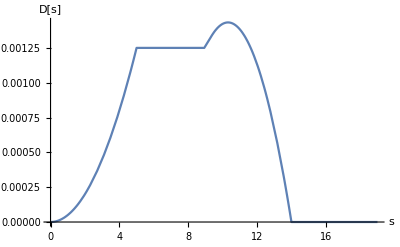

```mathematica
Plot[dispersion[x]//.focus//.{L ->5, rho-> 10000, d-> 2}, {x, 0, 19}, AxesLabel-> {"s", "D[s]"}]
```

```mathematica
slope[s_]=Piecewise[{{fordisp[s][[1,2]], s<=L}, {fordisp[s-L][[2,2]], L<s<=L+d}, {fordisp[s-L -d][[3,2]], L+d<s<=L+2*d}, {fordisp[s-L -2d][[4,2]], L+2*d<s<=2*L+2*d}, {(mBend.{0,0,1})[[2]], s > 2(L+d)}}];
```

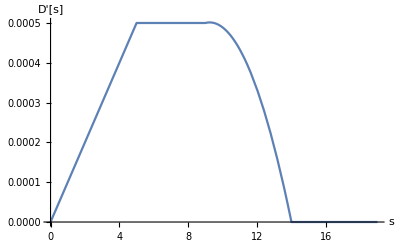

```mathematica
Plot[slope[x]//.focus//.{L ->5, rho-> 10000, d-> 2}, {x, 0, 19}, AxesLabel-> {"s", "D'[s]"}]
```